Plot $\Gamma$

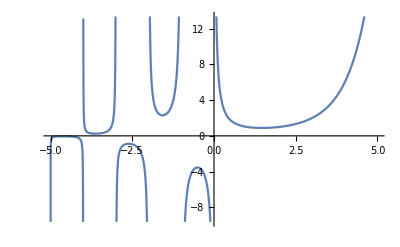

```mathematica
Plot[Gamma[z],{z,-5,5}]
```

```mathematica
ComplexPlot[Gamma[z],{z,-5-5I,5+5I}]
```

-Graphics-

```mathematica
Plot3D[Im@Gamma[x+y*I],{x,-5,5},{y,-5,5}]
```

-Graphics3D-

```mathematica
Series[Gamma[ϵ],{ϵ,0,2}]/.EulerGamma->Subscript[γ,Eu]
```

1/ϵ-γ_Eu+1/12 (π^2+6 γ_Eu^2) ϵ+1/6 (PolyGamma[2,1]-(π^2 γ_Eu)/2-γ_Eu^3) ϵ^2+O[ϵ]^3

```mathematica
Series[Gamma[ϵ+1],{ϵ,0,2}]/.EulerGamma->Subscript[γ,Eu]
```

1-γ_Eu ϵ+1/12 (π^2+6 γ_Eu^2) ϵ^2+O[ϵ]^3

```mathematica
Series[Gamma[ϵ+1]*Exp[ϵ*Subscript[γ, Eu]],{ϵ,0,3}]/.EulerGamma->Subscript[γ,Eu]
```

1+(π^2 ϵ^2)/12+1/6 PolyGamma[2,1] ϵ^3+O[ϵ]^4

```mathematica
A = Series[Exp[e*EulerGamma]*Gamma[e],{e,0,2}]//FunctionExpand//Expand
```

1/e+(π^2 e)/12-1/3 Zeta[3] e^2+O[e]^3

```mathematica
Series[Gamma[e],{e,0,2}]//Normal//FunctionExpand//Expand//Simplify
```

1/e-EulerGamma+1/12 e (6 EulerGamma^2+π^2)-1/12 e^2 (2 EulerGamma^3+EulerGamma π^2+4 Zeta[3])

```mathematica
Series[Gamma[1+e],{e,0,2}]//Normal//FunctionExpand//Expand//Simplify
```

1-e EulerGamma+1/12 e^2 (6 EulerGamma^2+π^2)

```mathematica
Collect[Series[Exp[e*EulerGamma]*Gamma[1+e],{e,0,3}]//Normal//FunctionExpand//Expand,e]
```

1+(e^2 π^2)/12-1/3 e^3 Zeta[3]

```mathematica
B = Series[Exp[-e*Log[-p2]],{e,0,2}]
```

1-Log[-p2] e+1/2 Log[-p2]^2 e^2+O[e]^3

```mathematica
A*B
```

1/e-Log[-p2]+(π^2/12+1/2 Log[-p2]^2) e+O[e]^2

```mathematica
Plot3D[Im@Log[x+y*I],{x,-2,2},{y,-2,2}]
```

-Graphics3D-

```mathematica
c= Series[Gamma[1-e],{e,0,2}]//Normal//FunctionExpand//Expand//Simplify
```

1+e EulerGamma+1/12 e^2 (6 EulerGamma^2+π^2)

```mathematica
d= Series[Gamma[2-e],{e,0,2}]//Normal//FunctionExpand//Expand//Simplify
```

1+e (-1+EulerGamma)+1/12 e^2 (-12 EulerGamma+6 EulerGamma^2+π^2)

```mathematica
f=Series[Gamma[3-2*e],{e,0,2}]//Normal//FunctionExpand//Expand//Simplify
```

2+e (-6+4 EulerGamma)+2/3 e^2 (6-18 EulerGamma+6 EulerGamma^2+π^2)

```mathematica
A*B*c*d/f
```

1/(2 e)+(1/2 (3-2 EulerGamma)+1/2 (-1+EulerGamma)+1/2 (EulerGamma-Log[-p2]))+(1/6 (21-18 EulerGamma+6 EulerGamma^2-π^2)+1/24 (-12 EulerGamma+6 EulerGamma^2+π^2)+(-1+EulerGamma) (1/2 (3-2 EulerGamma)+1/2 (EulerGamma-Log[-p2]))+1/2 (3-2 EulerGamma) (EulerGamma-Log[-p2])+1/2 (π^2/12+1/12 (6 EulerGamma^2+π^2)-EulerGamma Log[-p2]+1/2 Log[-p2]^2)) e+O[e]^2